# Hironaka’s Example: Finding the normalized dilatations of filled subspaces

## Hoping to find out whether there are finitely many or infinitely many subspaces with filled normalized dilatations less than the minimizer for Hironaka’s 3-manifold.

## Set up functions

First we set up function that, given a primitive integral class  in the fibered cone in Hironaka’s example, compute the genus , the number of boundary components , and the dilatation  as per Hironaka Proposition 3.4, Proposition 3.3, and Proposition 3.1 respectively.

```mathematica
genus[a_,b_]:=Module[{genus},
						If[GCD[3,a*b]==1, genus=b, genus=b-1];
						genus]
boundary[a_,b_]:=Module[{boundary},
						If[GCD[3,a*b]==1, boundary=2, boundary=4];
						boundary]
dila[a_,b_]:=Module[{theta},
				theta[t_]=Power[t,2*b]-t^b(1+t^a+Power[t,-a])+1;
				Max[Abs[t/.Solve[theta[t]==0,t, Reals]]]]
```

## Normalized dilatation functions

Next we compute the normalized dilatation  of an unfilled class primitive class  in three different ways.
The first function does this first by computing the dilatation  as the largest real root (in absolute value) of the corresponding Teichmuller polynomial:  (Hironaka Proposition 3.1).
Then it computes the Thurston norm:  (Hironaka Equation 2).
Finally, the normalized dilatation is .

```mathematica
normDilaUnfilled1[a_,b_]:= 2*b*Log[dila[a,b]]
```

The second function accomplishes the same task in a very similar manner, however instead of using the Thurston norm directly, it is computed indirectly by calculating the genus ( if  and  if  (Hironaka Proposition 3.4)) and the number of boundary components ( if  and  if  (Hironaka Proposition 3.3)).
The Thurston norm is then .
This version is less desirable than the first because it requires more calculations and it can only be carried out with integer classes due to the gcd computations.

```mathematica
normDilaUnfilled2[a_,b_]:= (2*genus[a,b]+boundary[a,b]-2)*Log[dila[a,b]]
```

The third function takes a slightly different approach.
We use the fact that the normalized dilatation is constant on rays through the origin (Hironaka Corollary 2.3).
First, we find the level set where  by solving for when  which is equivalent to solving the equation  and writing this as a function of :

```mathematica
levelset[a_]:=b/.Solve[Exp[2b]-Exp[b]*(1+Exp[a]+Exp[-a])+1==0,b,Reals][[2]]
```

We graph this level set below together with the boundary of the fibered cone in question.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

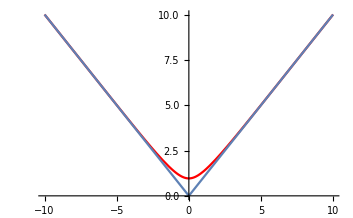

```mathematica
p1=Plot[levelset[a], {a,-10,10}, PlotStyle->Red];
p2=Plot[Abs[a],{a,-10,10}];
Show[p1,p2]
```

On this level set, the normalized dilatation just the Thurston norm.
Therefore, to compute the normalized dilatation for a class  we must find the intersection point of the ray through  and  and the above level set.
The normalized dilatation is the the Thurston norm of the (y value of) this intersection point.
(This seems to be the most computationally expensive method).

```mathematica
normDilaUnfilled3[a_,b_]:=Module[{xval},
									xval=x/.Solve[levelset[x]==(b/a)*x,x][[1]];
									2*levelset[xval]]
```

Now a quick check to make sure all three functions give us the same output at some test values:

```mathematica
N[normDilaUnfilled1[1,3]]==N[normDilaUnfilled2[1,3]]==N[normDilaUnfilled3[1,3]]
N[normDilaUnfilled1[5,9]]==N[normDilaUnfilled2[5,9]]==N[normDilaUnfilled3[5,9]]
N[normDilaUnfilled1[3,7]]==N[normDilaUnfilled2[3,7]]==N[normDilaUnfilled3[3,7]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

True

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

True

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

True

This next line shows the minimal normalized dilatation achieved in Hironaka’s example.

```mathematica
minimal=normDilaUnfilled1[0,1]
```

2 Log[1/2 (3+√5)]

Next we turn to computing the normalized dilatations of the filled in primitive classes .
The first method computed the dilatation as before, and then computes the genus as per Hironaka Proposition 3.4.
Then the normalized dilatation of  is .

```mathematica
normDilaFilled1[a_,b_]:= (2*genus[a,b]-2)*Log[dila[a,b]]
```

The second method, instead of computing the genus directly, uses the Thurston norm of the unfilled class and subtracts the number of boundary components as per Hironaka Proposition 3.3.

```mathematica
normDilaFilled2[a_,b_]:= (2*b-boundary[a,b])*Log[dila[a,b]]
```

And finally we have another function to compute the normalized dilatation of the filled in class by using any one of the three filled functions from before, dividing by the old Thurston norm and multiplying by the new one:

```mathematica
normDilaFilled3[a_,b_]:=normDilaUnfilled1[a,b]*(2*genus[a,b]-2)/(2*genus[a,b]+boundary[a,b]-2)
```

```mathematica
normDilaFilled1[1,3]==normDilaFilled2[1,3]==normDilaFilled3[1,3]
normDilaFilled1[5,9]==normDilaFilled2[5,9]==normDilaFilled3[5,9]
normDilaFilled1[3,7]==normDilaFilled2[3,7]==normDilaFilled3[3,7]
```

True

True

True

## Evidence for infinitely many filled in classes less than minimizer

Next we show evidence that there are infinitely many codimension one subspaces (lines) such that the filled in primitive class on that line has normalized dilatation less than Hironaka’s minimizer.
This corresponds to the idea that there are infinitely many subspaces whose filled in minimizer is smaller than the minimizer on the unfilled manifold.
In particular, the following plots show for  with for  that .

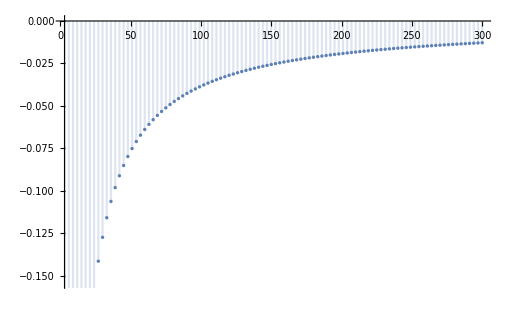
{215.67,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled1[1,b]-minimal,{b,3,300,3}]]
```

```mathematica
Timing[DiscretePlot[normDilaFilled1[1,b]-minimal,{b,3,300000,3}]]
```

{1443.15,-Graphics-}

The proof for such a claim would probably go something like as follows:
When , we get that  so that . Therefore .
Thus, . So  is equivalent to .
The issue is that it is very difficult to come up with an analytical expression for :

```mathematica
dila[1,b]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1+t^(2 b)-t^b (1+1/t+t)==0,t,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Abs[t/.Solve[1+t^(2 b)-t^b (1+1/t+t)==0,t,ℝ]]

The following were just tests to see which normalized dilatation computation is fastest. I guess the results aren’t surprising...

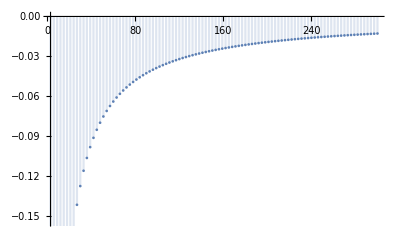
{197.822,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled1[1,b]-minimal,{b,3,300,3}]]
```

```mathematica
Timing[DiscretePlot[normDilaFilled2[1,b]-minimal,{b,3,300,3}]]
```

{203.631,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled3[1,b]-minimal,{b,3,300,3}]]
```

{205.112,-Graphics-}

```mathematica
Limit[dila[1,b],b->Infinity]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1+t^(2 b)-t^b (1+1/t+t)==0,t,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

lim_(b→∞) Abs[t/.Solve[1+t^(2 b)-t^b (1+1/t+t)==0,t,ℝ]]

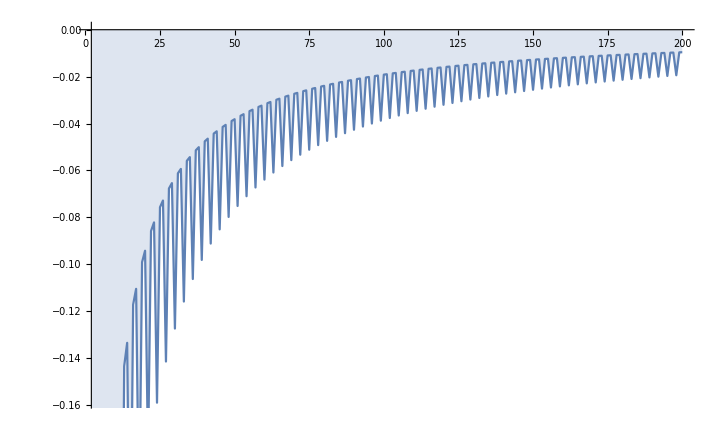
{92.853,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled1[1,b]-minimal,{b,2,200}]]
```

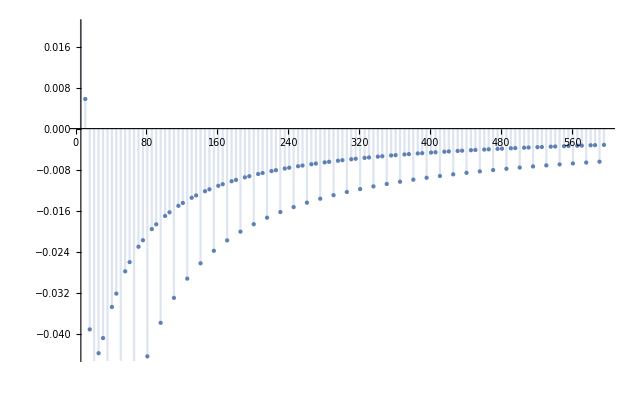
{465.652,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled1[5,b]-minimal,{b,6,600,5}]]
```

Here is just an example to show that not every sequence of filled in classes in less than the minimizer.

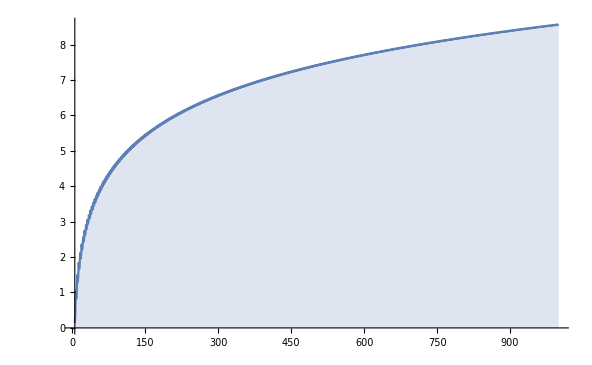
{3437.79,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled1[a,a+1]-minimal,{a,5,1000}]]
```